Calculating the critical point of the McCoy-Wu model for the binary distribution.

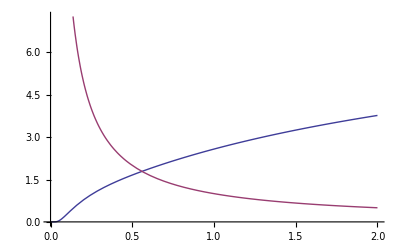

```mathematica
Plot[{Log[Coth[1/x]]+Log[Coth[0.1/x]],1/x},{x,0,2}]
```

```mathematica
FindRoot[Log[Coth[1/x]]+Log[Coth[0.05/x]]==4/x,{x,1}]
```

{x→1.1471}

```mathematica
FindRoot[Log[Coth[x-0.05]]+Log[Coth[x+0.05]]==4x,{x,1}]
```

{x→0.442454}

```mathematica
FindRoot[Log[Coth[x-0.1]]+Log[Coth[x+0.1]]==4x,{x,1}]
```

{x→0.447746}

```mathematica
FindRoot[Log[Coth[x*δ]]+Log[Coth[x/δ]]==4*x/.δ->1.8,{x,1}]
```

{x→0.451041}

Calculating the critical point of the McCoy-Wu model for the recangular distribution. First I Calculate the integral in the expression for the critical point with rectangular probability distribution and then I find the intersection of the transcendental equation.

```mathematica
Integrate[1/0.1(HeavisideTheta[x-(J-0.05)]-HeavisideTheta[x-(J+0.05)])*Log[Tanh[x]],{x,0,Infinity},Assumptions->J∈Reals&&J>0]
```

ConditionalExpression[4.11234+5. Log[Tanh[0.05+J]] Log[1.+1. Tanh[0.05+J]]+10. (-1/8 π^2 HeavisideTheta[0.05-J]+0.5 (-1.+HeavisideTheta[0.05-J]) (0.822467+1. Log[1.-1. Tanh[0.05-1. J]] Log[-Tanh[0.05-1. J]]+1. PolyLog[2.,Tanh[0.05-1. J]]+1. PolyLog[2.,1.+Tanh[0.05-1. J]]))+5. PolyLog[2.,1.-1. Tanh[0.05+J]]+5. PolyLog[2.,-1. Tanh[0.05+J]],J≥0.05]

```mathematica
FindRoot[4.112335167120566+5. Log[Tanh[0.05+J]] Log[1.+1. Tanh[0.05+J]]+10. (-1/8 π^2 HeavisideTheta[0.05-J]+0.5 (-1.+HeavisideTheta[0.05-J]) (0.8224670334241132+1. Log[1.-1. Tanh[0.05-1. J]] Log[-Tanh[0.05-1. J]]+1. PolyLog[2.,Tanh[0.05-1. J]]+1. PolyLog[2.,1.+Tanh[0.05-1. J]]))+5. PolyLog[2.,1.-1. Tanh[0.05+J]]+5. PolyLog[2.,-1. Tanh[0.05+J]]==-2J,{J,1}]
```

{J→0.441277}

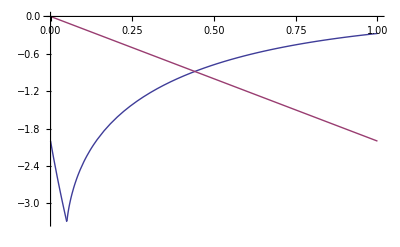

```mathematica
Plot[{4.112335167120566+5. Log[Tanh[0.05+J]] Log[1.+1. Tanh[0.05+J]]+10. (-1/8 π^2 HeavisideTheta[0.05-J]+0.5 (-1.+HeavisideTheta[0.05-J]) (0.8224670334241132+1. Log[1.-1. Tanh[0.05-1. J]] Log[-Tanh[0.05-1. J]]+1. PolyLog[2.,Tanh[0.05-1. J]]+1. PolyLog[2.,1.+Tanh[0.05-1. J]]))+5. PolyLog[2.,1.-1. Tanh[0.05+J]]+5. PolyLog[2.,-1. Tanh[0.05+J]],-2J},{J,0,1}]
```

```mathematica
Integrate[1/0.4(HeavisideTheta[x-(J-0.2)]-HeavisideTheta[x-(J+0.2)])*Log[Tanh[x]],{x,0,Infinity},Assumptions->J∈Reals&&J>0]
```

ConditionalExpression[1.02808+1.25 Log[Tanh[0.2+J]] Log[1.+1. Tanh[0.2+J]]+2.5 (-1/8 π^2 HeavisideTheta[0.2-J]+0.5 (-1.+HeavisideTheta[0.2-J]) (0.822467+1. Log[1.-1. Tanh[0.2-1. J]] Log[-Tanh[0.2-1. J]]+1. PolyLog[2.,Tanh[0.2-1. J]]+1. PolyLog[2.,1.+Tanh[0.2-1. J]]))+1.25 PolyLog[2.,1.-1. Tanh[0.2+J]]+1.25 PolyLog[2.,-1. Tanh[0.2+J]],J≥0.2]

```mathematica
FindRoot[1.0280837917801415+1.25 Log[Tanh[0.2+J]] Log[1.+1. Tanh[0.2+J]]+2.5 (-1/8 π^2 HeavisideTheta[0.2-J]+0.5 (-1.+HeavisideTheta[0.2-J]) (0.8224670334241132+1. Log[1.-1. Tanh[0.2-1. J]] Log[-Tanh[0.2-1. J]]+1. PolyLog[2.,Tanh[0.2-1. J]]+1. PolyLog[2.,1.+Tanh[0.2-1. J]]))+1.25 PolyLog[2.,1.-1. Tanh[0.2+J]]+1.25 PolyLog[2.,-1. Tanh[0.2+J]]==-2J,{J,1}]
```

{J→0.450341}

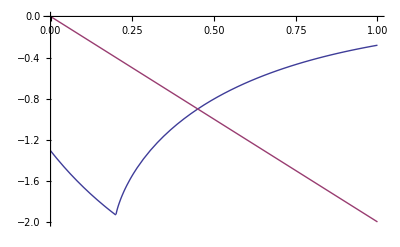

```mathematica
Plot[{1.0280837917801415+1.25 Log[Tanh[0.2+J]] Log[1.+1. Tanh[0.2+J]]+2.5 (-1/8 π^2 HeavisideTheta[0.2-J]+0.5 (-1.+HeavisideTheta[0.2-J]) (0.8224670334241132+1. Log[1.-1. Tanh[0.2-1. J]] Log[-Tanh[0.2-1. J]]+1. PolyLog[2.,Tanh[0.2-1. J]]+1. PolyLog[2.,1.+Tanh[0.2-1. J]]))+1.25 PolyLog[2.,1.-1. Tanh[0.2+J]]+1.25 PolyLog[2.,-1. Tanh[0.2+J]],-2J},{J,0,1}]
```

```mathematica
Integrate[1/0.2(HeavisideTheta[x-(J-0.1)]-HeavisideTheta[x-(J+0.1)])*Log[Tanh[x]],{x,0,Infinity},Assumptions->J∈Reals&&J>0]
```

ConditionalExpression[2.05617+2.5 Log[Tanh[0.1+J]] Log[1.+1. Tanh[0.1+J]]+5. (-1/8 π^2 HeavisideTheta[0.1-J]+0.5 (-1.+HeavisideTheta[0.1-J]) (0.822467+1. Log[1.-1. Tanh[0.1-1. J]] Log[-Tanh[0.1-1. J]]+1. PolyLog[2.,Tanh[0.1-1. J]]+1. PolyLog[2.,1.+Tanh[0.1-1. J]]))+2.5 PolyLog[2.,1.-1. Tanh[0.1+J]]+2.5 PolyLog[2.,-1. Tanh[0.1+J]],J≥0.1]

```mathematica
FindRoot[2.056167583560283+2.5 Log[Tanh[0.1+J]] Log[1.+1. Tanh[0.1+J]]+5. (-1/8 π^2 HeavisideTheta[0.1-J]+0.5 (-1.+HeavisideTheta[0.1-J]) (0.8224670334241132+1. Log[1.-1. Tanh[0.1-1. J]] Log[-Tanh[0.1-1. J]]+1. PolyLog[2.,Tanh[0.1-1. J]]+1. PolyLog[2.,1.+Tanh[0.1-1. J]]))+2.5 PolyLog[2.,1.-1. Tanh[0.1+J]]+2.5 PolyLog[2.,-1. Tanh[0.1+J]]==-2J,{J,1}]
```

{J→0.443057}

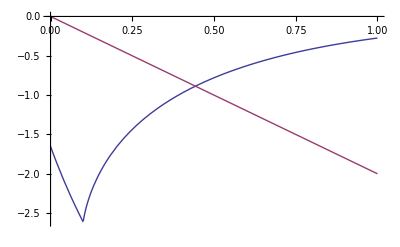

```mathematica
Plot[{2.056167583560283+2.5 Log[Tanh[0.1+J]] Log[1.+1. Tanh[0.1+J]]+5. (-1/8 π^2 HeavisideTheta[0.1-J]+0.5 (-1.+HeavisideTheta[0.1-J]) (0.8224670334241132+1. Log[1.-1. Tanh[0.1-1. J]] Log[-Tanh[0.1-1. J]]+1. PolyLog[2.,Tanh[0.1-1. J]]+1. PolyLog[2.,1.+Tanh[0.1-1. J]]))+2.5 PolyLog[2.,1.-1. Tanh[0.1+J]]+2.5 PolyLog[2.,-1. Tanh[0.1+J]],-2J},{J,0,1}]
```

```mathematica
Integrate[1/0.8(HeavisideTheta[x-(J-0.4)]-HeavisideTheta[x-(J+0.4)])*Log[Tanh[x]],{x,0,Infinity},Assumptions->J∈Reals&&J>0]
```

ConditionalExpression[0.514042+0.625 Log[Tanh[0.4+J]] Log[1.+1. Tanh[0.4+J]]+1.25 (-1/8 π^2 HeavisideTheta[0.4-J]+0.5 (-1.+HeavisideTheta[0.4-J]) (0.822467+1. Log[1.-1. Tanh[0.4-1. J]] Log[-Tanh[0.4-1. J]]+1. PolyLog[2.,Tanh[0.4-1. J]]+1. PolyLog[2.,1.+Tanh[0.4-1. J]]))+0.625 PolyLog[2.,1.-1. Tanh[0.4+J]]+0.625 PolyLog[2.,-1. Tanh[0.4+J]],J≥0.4]

```mathematica
FindRoot[0.5140418958900708+0.625 Log[Tanh[0.4+J]] Log[1.+1. Tanh[0.4+J]]+1.25 (-1/8 π^2 HeavisideTheta[0.4-J]+0.5 (-1.+HeavisideTheta[0.4-J]) (0.8224670334241132+1. Log[1.-1. Tanh[0.4-1. J]] Log[-Tanh[0.4-1. J]]+1. PolyLog[2.,Tanh[0.4-1. J]]+1. PolyLog[2.,1.+Tanh[0.4-1. J]]))+0.625 PolyLog[2.,1.-1. Tanh[0.4+J]]+0.625 PolyLog[2.,-1. Tanh[0.4+J]]==-2J,{J,1}]
```

{J→0.482915}

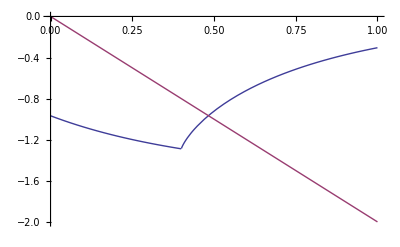

```mathematica
Plot[{0.5140418958900708+0.625 Log[Tanh[0.4+J]] Log[1.+1. Tanh[0.4+J]]+1.25 (-1/8 π^2 HeavisideTheta[0.4-J]+0.5 (-1.+HeavisideTheta[0.4-J]) (0.8224670334241132+1. Log[1.-1. Tanh[0.4-1. J]] Log[-Tanh[0.4-1. J]]+1. PolyLog[2.,Tanh[0.4-1. J]]+1. PolyLog[2.,1.+Tanh[0.4-1. J]]))+0.625 PolyLog[2.,1.-1. Tanh[0.4+J]]+0.625 PolyLog[2.,-1. Tanh[0.4+J]],-2J},{J,0,1}]
```

Width 1.0

```mathematica
Integrate[1/1.0(HeavisideTheta[x-(J-0.5)]-HeavisideTheta[x-(J+0.5)])*Log[Tanh[x]],{x,0,Infinity},Assumptions->J∈Reals&&J>0]
```

ConditionalExpression[0.411234+0.5 Log[Tanh[0.5+J]] Log[1.+1. Tanh[0.5+J]]+1. (-1/8 π^2 HeavisideTheta[0.5-J]+0.5 (-1.+HeavisideTheta[0.5-J]) (0.822467+1. Log[1.-1. Tanh[0.5-1. J]] Log[-Tanh[0.5-1. J]]+1. PolyLog[2.,Tanh[0.5-1. J]]+1. PolyLog[2.,1.+Tanh[0.5-1. J]]))+0.5 PolyLog[2.,1.-1. Tanh[0.5+J]]+0.5 PolyLog[2.,-1. Tanh[0.5+J]],J≥0.5]

```mathematica
FindRoot[0.4112335167120566+0.5 Log[Tanh[0.5+J]] Log[1.+1. Tanh[0.5+J]]+1. (-1/8 π^2 HeavisideTheta[0.5-J]+0.5 (-1.+HeavisideTheta[0.5-J]) (0.8224670334241132+1. Log[1.-1. Tanh[0.5-1. J]] Log[-Tanh[0.5-1. J]]+1. PolyLog[2.,Tanh[0.5-1. J]]+1. PolyLog[2.,1.+Tanh[0.5-1. J]]))+0.5 PolyLog[2.,1.-1. Tanh[0.5+J]]+0.5 PolyLog[2.,-1. Tanh[0.5+J]]==-2J,{J,1}]
```

{J→0.514014}

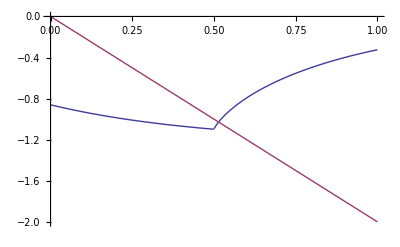

```mathematica
Plot[{0.4112335167120566+0.5 Log[Tanh[0.5+J]] Log[1.+1. Tanh[0.5+J]]+1. (-1/8 π^2 HeavisideTheta[0.5-J]+0.5 (-1.+HeavisideTheta[0.5-J]) (0.8224670334241132+1. Log[1.-1. Tanh[0.5-1. J]] Log[-Tanh[0.5-1. J]]+1. PolyLog[2.,Tanh[0.5-1. J]]+1. PolyLog[2.,1.+Tanh[0.5-1. J]]))+0.5 PolyLog[2.,1.-1. Tanh[0.5+J]]+0.5 PolyLog[2.,-1. Tanh[0.5+J]],-2J},{J,0,1}]
```

Width 0.5

```mathematica
Integrate[1/0.5(HeavisideTheta[x-(J-0.25)]-HeavisideTheta[x-(J+0.25)])*Log[Tanh[x]],{x,0,Infinity},Assumptions->J∈Reals&&J>0]
```

ConditionalExpression[0.822467+1. Log[Tanh[0.25+J]] Log[1.+1. Tanh[0.25+J]]+2. (-1/8 π^2 HeavisideTheta[0.25-J]+0.5 (-1.+HeavisideTheta[0.25-J]) (0.822467+1. Log[1.-1. Tanh[0.25-1. J]] Log[-Tanh[0.25-1. J]]+1. PolyLog[2.,Tanh[0.25-1. J]]+1. PolyLog[2.,1.+Tanh[0.25-1. J]]))+1. PolyLog[2.,1.-1. Tanh[0.25+J]]+1. PolyLog[2.,-1. Tanh[0.25+J]],J≥0.25]

```mathematica
FindRoot[0.8224670334241132+1. Log[Tanh[0.25+J]] Log[1.+1. Tanh[0.25+J]]+2. (-1/8 π^2 HeavisideTheta[0.25-J]+0.5 (-1.+HeavisideTheta[0.25-J]) (0.8224670334241132+1. Log[1.-1. Tanh[0.25-1. J]] Log[-Tanh[0.25-1. J]]+1. PolyLog[2.,Tanh[0.25-1. J]]+1. PolyLog[2.,1.+Tanh[0.25-1. J]]))+1. PolyLog[2.,1.-1. Tanh[0.25+J]]+1. PolyLog[2.,-1. Tanh[0.25+J]]==-2J,{J,0.5}]
```

{J→0.455991}

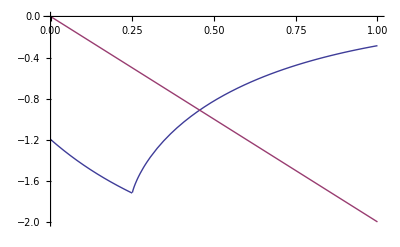

```mathematica
Plot[{0.8224670334241132+1. Log[Tanh[0.25+J]] Log[1.+1. Tanh[0.25+J]]+2. (-1/8 π^2 HeavisideTheta[0.25-J]+0.5 (-1.+HeavisideTheta[0.25-J]) (0.8224670334241132+1. Log[1.-1. Tanh[0.25-1. J]] Log[-Tanh[0.25-1. J]]+1. PolyLog[2.,Tanh[0.25-1. J]]+1. PolyLog[2.,1.+Tanh[0.25-1. J]]))+1. PolyLog[2.,1.-1. Tanh[0.25+J]]+1. PolyLog[2.,-1. Tanh[0.25+J]],-2J},{J,0,1}]
```